```mathematica
(*Jacobi4-primetheorem*)
Solvei[p_]:=Module[{qq,res},
For[qq=0,qq<=p-1,qq++,
If[Mod[qq^2,p]==p-1,res=qq];];
res
];
Solve4prime[p_]:=Module[{a0,a1,a2,a3,resultset},
resultset={};
For[a0=1,a0<=p,a0=a0+2,
For[a1=-p-1,a1<=p,a1=a1+2,
For[a2=-p-1,a2<=p,a2=a2+2,
For[a3=-p-1,a3<=p,a3=a3+2,
If[a0^2+a1^2+a2^2+a3^2==p,resultset=Append[resultset,{a0,a1,a2,a3}];
];
];
];
];
];
resultset
];
```

```mathematica
generatingpqeven[max_]:=Module[{result,pp,qq,p,q},
result={};
For[pp=1,pp<=max,pp++,
For[qq=1,qq<=max,qq++,
p=Prime[pp];
q=Prime[qq];
If[Mod[p,4]==1&&Mod[q,4]==1&&p!=q&&JacobiSymbol[p,q]==1,result=Append[result,{p,q}];];
];
];
result
];
generatingpqodd[max_]:=Module[{result,pp,qq,p,q},
result={};
For[pp=1,pp<=max,pp++,
For[qq=1,qq<=max,qq++,
p=Prime[pp];
q=Prime[qq];
If[Mod[p,4]==1&&Mod[q,4]==1&&p!=q&&JacobiSymbol[p,q]==-1,result=Append[result,{p,q}];];
];
];
result
];
```

```mathematica
(*generatingPGL*)
equivalencePGL[A_,B_,p_]:=Module[{result,ii},
result=0;
For[ii=1,ii<=p,ii++,
If[Mod[A-ii B,p]=={{0,0},{0,0}},result=1];
];
result
];
quaunit[p_]:=quaunit[p]=Module[{ii,result},
result={1};
For[ii=2,ii<=p,ii++,
If[Mod[ii^2,p]==1,result=Append[result,ii];]
];
Mod[result,p]
];
numberofquaunit[p_]:=numberofquaunit[p]=Length[quaunit[p]];
equivalencePSL[A_,B_,p_]:=Module[{result,ii},
result=0;
For[ii=1,ii<=numberofquaunit[p],ii++,
If[Mod[A-quaunit[p][[ii]] B,p]=={{0,0},{0,0}},result=1];
];
result
];
PGL[p_]:=Module[{a11,a12,a21,a22,result,AAtest,outputlist,Le,flag,totalset,testtt},
result={({{1, 0}, {0, 1}})};
totalset=Table[i,{i,0,p-1}];
(*For[testtt=1,(testtt<=Delta)&&(Length[result]<p (-1+p^2)),testtt++,
If[Mod[testtt,100]==1,Print[{testtt,N[Length[result]/(p (-1+p^2))]}]];*)
For[a11=1,a11<=p,a11++,
For[a12=1,a12<=p,a12++,
Print[{a11,a12}];
For[a21=1,a21<=p,a21++,
For[a22=1,a22<=p,a22++,
outputlist=1;
AAtest=({{a11, a12}, {a21, a22}});
If[Mod[Det[AAtest],p]==0,outputlist=0,Le=Length@result;
For[flag=1,flag<=Le,flag++,
If[equivalencePGL[AAtest,result[[flag]],p]==1,outputlist=0;Break[];];
];
If[outputlist==1,result=Append[result,Mod[AAtest,p]];];];
];
];
];
];
result
];
PSL[p_]:=Module[{a11,a12,a21,a22,result,AAtest,outputlist,Le,flag,totalset,testtt},
result={({{1, 0}, {0, 1}})};
totalset=Table[i,{i,0,p-1}];
(*For[testtt=1,(testtt<=Delta)&&(Length[result]<(p (-1+p^2)/numberofquaunit[p])),testtt++,
If[Mod[testtt,100]==1,Print[{testtt,N[Length[result]/((p (-1+p^2)/numberofquaunit[p]))]}]];*)
For[a11=1,a11<=p,a11++,
For[a12=1,a12<=p,a12++,
Print[{a11,a12}];
For[a21=1,a21<=p,a21++,
For[a22=1,a22<=p,a22++,
outputlist=1;
AAtest=({{a11, a12}, {a21, a22}});
If[Mod[Det[AAtest],p]!=1,outputlist=0,Le=Length@result;
For[flag=1,flag<=Le,flag++,
If[equivalencePSL[AAtest,result[[flag]],p]==1,outputlist=0;Break[];];
];
If[outputlist==1,result=Append[result,Mod[AAtest,p]];];];
];
];
];
];
result
];
```

```mathematica
(*set5=PGL[5];
set52=PSL[5];
set13=PGL[13];
set132=PSL[13];
Export[NotebookDirectory[]<>"someplgroups.m",{set5,set52,set13,set132}];*)
```

```mathematica
{set5,set52,set13,set132}=Import[NotebookDirectory[]<>"someplgroups.m"];
```

```mathematica
generatingpqeven[20]
generatingpqodd[20]
```

{{5,29},{5,41},{5,61},{13,17},{13,29},{13,53},{13,61},{17,13},{17,53},{29,5},{29,13},{29,53},{37,41},{37,53},{41,5},{41,37},{41,61},{53,13},{53,17},{53,29},{53,37},{61,5},{61,13},{61,41}}

{{5,13},{5,17},{5,37},{5,53},{13,5},{13,37},{13,41},{17,5},{17,29},{17,37},{17,41},{17,61},{29,17},{29,37},{29,41},{29,61},{37,5},{37,13},{37,17},{37,29},{37,61},{41,13},{41,17},{41,29},{41,53},{53,5},{53,41},{53,61},{61,17},{61,29},{61,37},{61,53}}

```mathematica
generator[i_,p_,q_]:=Module[{aset,alphatildeset},
aset=Solve4prime[p];

alphatildeset=Table[({{aa[[1]]+i aa[[2]], aa[[3]]+i aa[[4]]}, {-aa[[3]]+i aa[[4]], aa[[1]]-i aa[[2]]}}),{aa,aset}];
Mod[alphatildeset,q]
];
```

```mathematica
searchPGL[generator_,large_,q_]:=Module[{Le,qq,res},
Le=Length@large;
For[qq=1,qq<=Le,qq++,
If[equivalencePGL[generator,large[[qq]],q]==1,res=qq;Break[];];
];
res
];
searchPSL[generator_,large_,q_]:=Module[{Le,qq,res},
Le=Length@large;
For[qq=1,qq<=Le,qq++,
If[equivalencePSL[generator,large[[qq]],q]==1,res=qq;Break[];];
];
res
];
```

```mathematica
(*p=13,q=5*)
pnow=13;(*17,37,53: PGL*)(*29,41,61: PSL*)
qnow=5;
inow=Solvei[qnow];
largenow=set5;(*PSL: set52*)
generatornow=generator[Solvei[qnow],pnow,qnow];
Length @ largenow

generatornowlabel=Table[searchPGL[generatorq,largenow,qnow],{generatorq,generatornow}]
```

120

{111,108,107,114,13,37,45,69,98,14,50,26,62,99}

```mathematica
(*groupstructure=Table[If[Mod[i,20]==1&&Mod[j,20]==1,Print[{i,j}]];searchPGL[largenow[[i]].largenow[[j]],largenow,qnow],{i,1,Length@largenow},{j,1,Length@largenow}];*)
```

```mathematica
groupstructure=Import[NotebookDirectory[]<>"groupstructureset5.m"];
```

```mathematica
groupstructure[[3, 4]]
(*Export[NotebookDirectory[]<>"groupstructureset5.m",groupstructure]*)
```

89

```mathematica
(*Draw 4-fold left-right Cayley graph*)
singlesize=Length@largenow;
basics[lab_]:=Table[{i,lab},{i,1,singlesize}];
add[A_]:=Table[{i,A[[i]]},{i,1,Length@A}];
nodes=add@Join[Join[Join[basics[{0,0}],basics[{0,1}]],basics[{1,0}]],basics[{1,1}]];
totalsize=Length@nodes;
```

```mathematica
E0star=DeleteDuplicates@Flatten[Table[{g,groupstructure[[g,b]]+singlesize},{g,1,singlesize},{b,generatornowlabel}],1];
Estar0=DeleteDuplicates@Flatten[Table[{g,groupstructure[[a,g]]+2singlesize},{g,1,singlesize},{a,generatornowlabel}],1];
```

```mathematica
Estar1=DeleteDuplicates@Flatten[Table[{groupstructure[[g,b]]+singlesize,groupstructure[[a,groupstructure[[g,b]]]]+3singlesize},{g,1,singlesize},{a,generatornowlabel},{b,generatornowlabel}],2];
E1star=DeleteDuplicates@Flatten[Table[{groupstructure[[a,g]]+2singlesize,groupstructure[[groupstructure[[a,g]],b]]+3singlesize},{g,1,singlesize},{a,generatornowlabel},{b,generatornowlabel}],2];
```

```mathematica
changetoedge[veclist_]:=Table[UndirectedEdge[qq[[1]],qq[[2]]],{qq,veclist}]
```

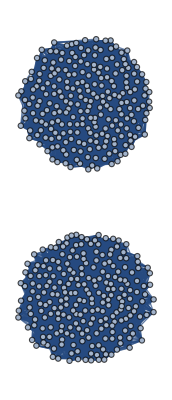

```mathematica
Graph[changetoedge[Join[E0star,Estar0,Estar1,E1star]]]
```